## the number of loops through a lattice

Walking on a lattice.  The number of various paths from (0,0) to (m,n)  using north and east steps is binomial coefficient (m+n
m). 
 if he needs to go back (0,0) using south and west steps, and doesn't pass by the passed points. Then what is the number of various loops walking from (0,0) to (m,n) then returning to (0,0)? Any algebraic expression for this?

ArrayPlot::mesh: Value of option Mesh -> Full is not All, None, n, or a valid list of mesh specifications; using All instead.

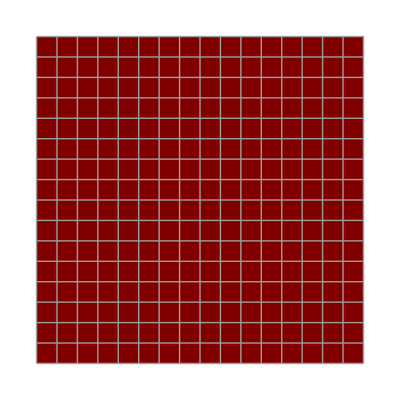

```mathematica
ArrayPlot[Array[1,{16,16}],Mesh->Full]
Needs["GraphUtilities`"];
GraphPlot[GridGraph[10,10],Method->None]
```

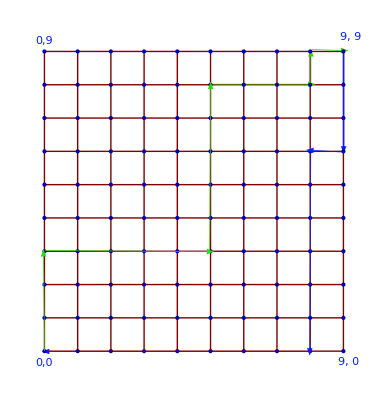

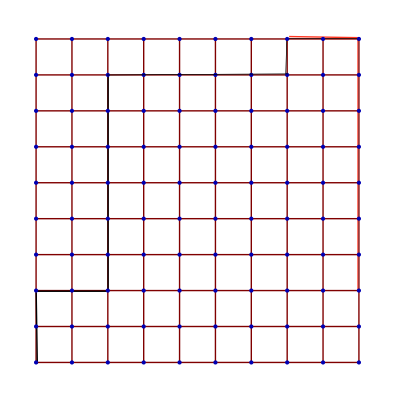

## a functin about tan x/2

Enter text here.

```mathematica
(*θ=Pi/3;*)
Plot3D[ (Sin[θ]/Tan [x* θ] -Cos[θ]),{x,0,8},{θ,-Pi,Pi}]
```

-Graphics3D-

## 质数的2-3-5分解形式不成立

71,119=7*17,157不能分解成以下形式之一

{2^i*3^j + 5^k, 2^i*5^k + 3^j, 2^i + 3^j*5^k}